# Data Science and Machine Learning II

## Author: Mathieu Bélanger Assignment 2: Cluster Analysis and API of the Green Domestic Product

#### Merci encore une fois Boris pour ce devoir bien intéressant!!

In this assignment, you will keep on exploring the Green Domestic Product, trying to uncover patterns behind our data. Can we find geographic clusters shedding light on the results we obtained in Assignment 1?

Once you are done you have to submit your notebook here: https://moodle.epfl.ch/mod/assign/view.php?id=1220874
There is no quiz, so your grade will depend only on your notebook.
If there is need for further clarifications on the questions, after the assignment is released, we will update this file, so make sure you check the git repository for updates.
	Good luck!

## Clustering Analysis

```mathematica
ClearAll["Global`*"]
```

Import as a dataset the CSV file: "GrDP_results.csv".
You can directly Import from the GitHub link: 
"https://raw.githubusercontent.com/michalis0/MGT-529/main/Assignment/Assignment_2/GrDP_results.csv"

```mathematica
data = Import["C:\\Users\\mbela\\ecole\\MGT-529\\Assignment\\Assignment_2\\GrDP_results.csv", "Dataset", "HeaderLines" -> 1];
```

```mathematica
RandomSample[data, 5]
```

Question 1: 
Create a scatter plot of the log of external costs and the log of GDP (considering all countries and years).    [1 point]

```mathematica
(*Not entirely sure this is absolutely useful, but my intuition is that otherwise the clusering will be affected by the different scale in distances between External Costs and GDP (if in million)*)
LogOfMillion[x_]:= Log[1000000*x]
```

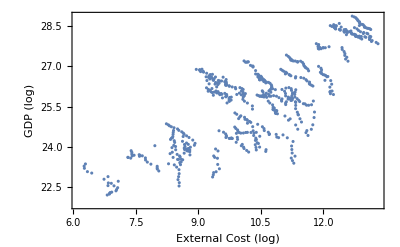

```mathematica
gdpCostLogs = data[All, {"External Cost" -> Log, "GDP [million Euro]" -> LogOfMillion}];
ListPlot[
gdpCostLogs[All, {"External Cost", "GDP [million Euro]"}],
Frame->True,
FrameLabel->{"External Cost (log)", "GDP (log)"}]
```

Question 2: 
Find clusters in our observations and visualize the results in a scatter plot.
I recommend using the log of external costs and log of GDP as variables, but feel free to use other variables, and even compute new ones (i.e., GDP per capita).
Feel free to explore different methods, number of clusters, and other options. [2 point]

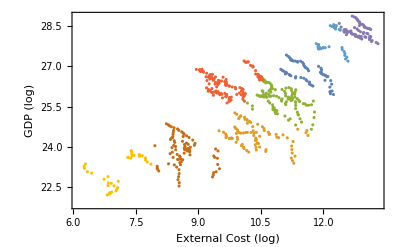

```mathematica
ListPlot[FindClusters[
Values @ gdpCostLogs[All, {"External Cost", "GDP [million Euro]"}], 8],
Frame->True,
FrameLabel->{"External Cost (log)", "GDP (log)"}]
```

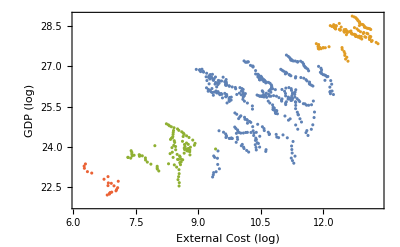

```mathematica
ListPlot[FindClusters[
Values @ gdpCostLogs[All, {"External Cost", "GDP [million Euro]"}],
Method -> "SpanningTree"],
Frame->True,
FrameLabel->{"External Cost (log)", "GDP (log)"}]
```

Question 3: 
Find the cluster in which your observations lie (i.e, clustering components). 
Create a new column in your original dataset, called "ClusterID" with the clustering components. 
You should use the same variables, method, number of clusters, etc. than in Question 2. [2 point]

```mathematica
clusterIDs = ClusteringComponents[
Normal @ gdpCostLogs[All, {"External Cost", "GDP [million Euro]"}],
8];
```

```mathematica
gdpCostLogs= Join[gdpCostLogs,  Transpose @ Dataset @ AssociationThread["ClusterID" -> {clusterIDs}], 2];
```

```mathematica
%[[;;5]]
```

Question 4: 
1) Extract a list of the countries belonging to your first cluster in 2000. 
2) Extract a list of the countries belonging to your first cluster in 2019.  [1 point]

```mathematica
cluster1Countries2000 = gdpCostLogs[Select[{#Year, #ClusterID} == {2000, 1}&], "Country"]
cluster1Countries2019 = gdpCostLogs[Select[{#Year, #ClusterID} == {2019, 1}&], "Country"]
```

Question 5: 
Find the evolution of Cluster ID for the country of your choice [1 point]

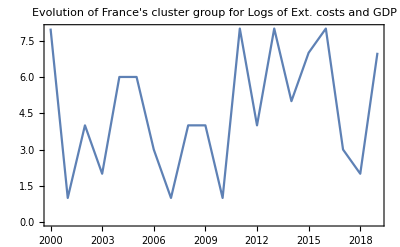

```mathematica
DateListPlot[TimeSeries[
Normal @ gdpCostLogs[Select[#Country == "France"&], "ClusterID"],
{"2000", "2019"}],
PlotLabel->"Evolution of France's cluster group for Logs of Ext. costs and GDP"
]
```

Question 6: 
For each cluster, calculate the mean of the variables you used for your cluster analysis.
For example, if you used the log of external costs and log of GDP, you should calculate, for each cluster, the mean of the log of external costs and the mean of the log of GDP.  [1 point]

```mathematica
gdpCostLogs[All, {"ClusterID", "External Cost", "GDP [million Euro]"}][GroupBy["ClusterID"],Mean]
```

```mathematica
groups[[1]][Mean, "External Cost"]
```

10.6566

Question 7:   
Create a Grid of maps showing your clusters in 2000, in 2010, and in 2019  [2 point]

```mathematica
countryEntities = Interpreter["Country"][#] & /@ Normal @ gdpCostLogs[Select[#Year == 2000&], "Country"];
```

```mathematica
clusterGrid = Grid @ List @ Map[Function[year,
GeoRegionValuePlot[AssociationThread[
countryEntities,
Normal @ gdpCostLogs[Select[#Year == year&], "ClusterID"]],
PlotLabel -> Style["Ext Costs vs. GDP Clusters (" <> ToString[year]  <> ")"]]],
{2000, 2010, 2019}
]
```

-Graphics- | -Graphics- | -Graphics-

Question 8:   
Deploy the result of Question 7 to the cloud. Set the permissions to public.  [1 point]

```mathematica
CloudPublish[clusterGrid, "WebServices/ExtCostGDPClustersGrid"]
```

CloudObject[https://www.wolframcloud.com/obj/mathieu.belanger/WebServices/ExtCostGDPClustersGrid]

## GrDP classifier API

Question 9:   
Create a (cluster) classifier function.
Display Information about your classifier function.
You do not need to use the same variables, method, number of clusters, etc. than in Question 2.  [2 point]

```mathematica
ExtCostGDPClassifier = ClusterClassify[
Normal @ gdpCostLogs[All, {"External Cost", "GDP [million Euro]"}],
8]
```

ClassifierFunction[…]

```mathematica
ClassifyExtCostGDPCluster[
totalExtCost_: _? (NumericQ),
GDP_: _?(NumericQ)] := ExtCostGDPClassifier[{totalExtCost, GDP}]

ClassifyExtCostGDPCluster::usage = "ClassifyExtCostGDPCluster[\!\(\*StyleBox[\"extCost\", \"TI\"]\), \!\(\*StyleBox[\"GDP\", \"TI\"]\)] returns the predicted cluster (from 1 to 8) for the datapoint. Input should be External costs and GDP of a given european country for a given year \n extCost: Total External costs of pollutants [euro] \n GDP: Gross domestic product [euro]";
```

```mathematica
Information[ClassifyExtCostGDPCluster]
```

```mathematica
ClassifierInformation[ExtCostGDPClassifier]
```

Classifier information
Data type | {Numerical,Numerical}
Number of classes | 8
Method | KMeans
Single evaluation time | 2.8 ms/example
Batch evaluation speed | 112. examples/ms
Model memory | 91.5 kB
Training examples used | 600 examples
Training time | 41.1 ms

Question 10:   
Create a local API function using your classifier.
For instance, if you used the log of external cost and log of GDP as variables to create your classifier, the API function should use as argument 2 numbers (log of external cost, log of GDP) and returns the cluster number. [2 point]

```mathematica
ExtCostGDPClusterAPI = APIFunction[{
"extCosts" -> "Number",
"GDP" -> "Number"
},
StringJoin[
"The cluster for this datapoint is: ",
ToString @ ClassifyExtCostGDPCluster[#extCosts, #GDP]
]&
];
```

```mathematica
ExtCostGDPClusterAPI[<|"extCosts"-> 5,"GDP" -> 5|>]
```

The cluster for this datapoint is: 6

Question 11:   
Deploy your API to the cloud, setting the permissions to public   [1 point]

```mathematica
CloudDeploy[ExtCostGDPClusterAPI, "WebServices/HTMLExtCostGDPClusterAPI", Permissions->"Public"]
```

CloudObject[https://www.wolframcloud.com/obj/mathieu.belanger/WebServices/HTMLExtCostGDPClusterAPI]

## [Advanced] GrDP information API

Question 12:   
Create a local API that takes as input the name of a country (as a string), and return as output:
- If the country belongs to our sample: a dataset containing the year, population, GDP, external cost, share of external cost, and GrDP per capita of our country.
- Else a string: "GrDP data is only available for the following country: {Belgium, Bulgaria, Czechia, Denmark, Germany, Estonia, Ireland, Greece, Spain, France, Croatia, Italy, Cyprus, Latvia, Lithuania, Luxembourg, Hungary, Malta, Netherlands, Austria, Poland, Portugal, Romania, Slovenia,  Slovakia, Finland, Sweden, Norway, Switzerland, United Kingdom}"  [2 points]
Tips: You can use the functions If to create conditional statement and MemberQ to check if an element belongs to a list.

```mathematica
data[[;;5]]
```

```mathematica
countryList = DeleteDuplicates @ data[All, "Country"];
```

```mathematica
getCountryGrDPData[country_] := If[MemberQ[countryList,country],
data[Select[#Country == country &], {"Year", "Population", "GDP [million Euro]", "External Cost", "Share External Cost", "GrDP per capita"}],
"GrDP data is only available for the following country: {Belgium, Bulgaria, Czechia, Denmark, Germany, Estonia, Ireland, Greece, Spain, France, Croatia, Italy, Cyprus, Latvia, Lithuania, Luxembourg, Hungary, Malta, Netherlands, Austria, Poland, Portugal, Romania, Slovenia,  Slovakia, Finland, Sweden, Norway, Switzerland, United Kingdom}"
]
```

```mathematica
(*Here the placeholder "Dummy" is used to make the query fail if no country is inputed*)
ExtCostGDPClusterAPI = APIFunction[{
"country" -> "String" -> "Dummy"
},
getCountryGrDPData[#country]&
];
```

```mathematica
ExtCostGDPClusterAPI[<| "country" -> "France" |>]
```